```mathematica
Remove["Global`*"]; (*clears all data before running*)
(*define and plot region for sprinkling*)
ρ=ImplicitRegion[t x≥0,{{x,0,1},{t,0,1}}];
η=ImplicitRegion[(t-1)(x-1)≤ 0,{{x,0,1},{t,0,1}}];
ϕ=RegionUnion[ρ,η];
RegionPlot[ϕ]
```

-Graphics-

```mathematica
(*pick n from a Poisson distribution centered around some mean*)
n=RandomVariate[PoissonDistribution[500]];
(*pick randomly n points from the defined region, and plot them*)
pt=RandomPoint[ϕ,n];//Timing
pt=Append[pt, {0.5,0}];
Show[RegionPlot[ϕ],Graphics[{PointSize[Small],Point[pt]},Axes->True]]
```

{0.0625,Null}

-Graphics-

```mathematica
(*find the causal matrix*)
pt=Sort[pt,#1[[2]]<#2[[2]]&];
c=Table[If[(pt[[i,2]]-pt[[j,2]])^2-(pt[[i,1]]-pt[[j,1]])^2>0,1,0],{i,n},{j,n}];
MatrixForm[c];
Subscript[c, u]=UpperTriangularize[c];
Subscript[Tc, u]=Transpose[Subscript[c, u]];
MatrixForm[Subscript[c, u]];
MatrixForm[Subscript[Tc, u]];
(*define the function A, which takes two elements as input and returns the cardinality of their order interval*)
A[a_,b_]:=Length[Intersection[Flatten[SparseArray[Subscript[c, u][[a]]]["NonzeroPositions"]],Flatten[SparseArray[Subscript[Tc, u][[b]]]["NonzeroPositions"]]]];
```

```mathematica
(*find the link matrix using powers of the causal matrix*)
pathCounts[am_?MatrixQ]:=With[{s=Developer`ToPackedArray@am},FixedPoint[s+#.s&,s,Length[am]]];
l=1-Unitize[pathCounts[Subscript[c, u]]-1];
MatrixForm[l];
(*define the function L, which takes an element as input and returns the list of elements linked to the former*)
L[p_] := Flatten[SparseArray[l[[p]]]["NonzeroPositions"]];
```

```mathematica
p0 =Flatten[Position[pt,{0.5,0}]][[1]]; (*initial point is defined. since the list of points are sorted wrt time, it automatically picks (0.5,0) as the initial point*)
```

```mathematica
(*pairs1 = Permutations[L[p0],{2}];
s=7;
q1=pairs1[[s,1]];
p1=pairs1[[s,2]];*)
```

```mathematica
(*listq2 = Intersection[L[q1],L[p1]];
validq2= Select[listq2,A[p0,#]==2&];
validp2= Select[L[p1],A[p0,#]==1&];*)
```

```mathematica
(*pairs2 = Tuples[{validq2,validp2}];
t=1;
q2=pairs2[[t,1]];
p2=pairs2[[t,2]];
pairs2*)
```

```mathematica
(*listq3 = Intersection[L[q2],L[p2]];
validq3= Select[listq3,A[p1,#]==2&];
validp3= Select[L[p2],A[p1,#]==1&];*)
```

```mathematica
(*pairs3 = Tuples[{validq3,validp3}];
u=1;
q3=pairs3[[u,1]];
p3=pairs3[[u,2]];*)
(*notice that the code for the 2nd and 3rd step are the same. subsequent steps can be gotten by repeating the same code, but that's inefficient. something like backtracking might help generate n-step ladders*)
```

```mathematica
(*generate atmost 3-step ladder*)
pairs1=Permutations[L[p0],{2}];
s=1;
q1=0;
p1=0;
q2=0;
p2=0;
q3=0;
p3=0;
qlist={};
plist={};
xx=0;
If[Length[pairs1]>0,
While[s≤ Length[pairs1],
q1=pairs1[[s,1]];
p1=pairs1[[s,2]];
listq2=Intersection[L[q1],L[p1]];
validq2=Select[listq2,A[p0,#]==2&];
validp2=Select[L[p1],A[p0,#]==1&];
pairs2=Tuples[{validq2,validp2}];
t=1;
If [Length[pairs2]>0,
While[t≤ Length[pairs2],
q2=pairs2[[t,1]];
p2=pairs2[[t,2]];
listq3=Intersection[L[q2],L[p2]];
validq3=Select[listq3,A[p1,#]==2&];
validp3=Select[L[p2],A[p1,#]==1&];
pairs3=Tuples[{validq3,validp3}];
If [Length[pairs3]>0,
q3=pairs3[[1,1]];
p3=pairs3[[1,2]];
qlist={q1,q2,q3};
plist={p1,p2,p3};
xx=xx+1;
Break[],
t=t+1;
];
];
];
If [xx>0,
Break[],
s=s+1;
];
];
];
pairs1
```

{{8,29},{8,108},{8,166},{29,8},{29,108},{29,166},{108,8},{108,29},{108,166},{166,8},{166,29},{166,108}}

```mathematica
qlist
```

{29,46,75}

```mathematica
plist
```

{8,24,36}

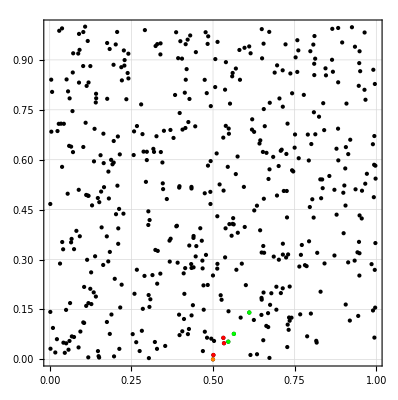

```mathematica
(*plot the sprinkling again, with the initial point coloured orange, p points coloured in red, and q points coloured in green*)
Graphics[{PointSize[Large],{Point[pt]},{Orange,Point[{pt[[p0]]}]},{Red,Point[{pt[[p1]],pt[[p2]],pt[[p3]]}]},{Green,Point[{pt[[q1]],pt[[q2]],pt[[q3]]}]}},Frame->True,GridLines->Automatic]
```

```mathematica
(*generate atmost 2-step ladder*)
(*pairs1=Permutations[L[p0],{2}];
s=1;
q1=0;
p1=0;
q2=0;
p2=0;
qlist={};
plist={};
If[Length[pairs1]>0,
While[s≤ Length[pairs1],
q1=pairs1[[s,1]];
p1=pairs1[[s,2]];
listq2=Intersection[L[q1],L[p1]];
validq2=Select[listq2,A[p0,#]==2&];
validp2=Select[L[p1],A[p0,#]==1&];
pairs2=Tuples[{validq2,validp2}];
If [Length[pairs2]>0,
q2=pairs2[[1,1]];
p2=pairs2[[1,2]];
qlist={q1,q2};
plist={p1,p2};
Break[],
s=s+1;
];
];
];
qlist
plist*)
```